Ejercicio 1:

```mathematica
Clear[f,alfa,beta, real,Riemann];

(* Valores personales *)
alfa = 4; (* Dia jueves *)
beta = 9;  (* Rol 2773029-9 *)

(* Funcion que se desea integrar *)
f[x_,y_] = x*y*ⅇ^(-alfa(x^2+y^2));

(* Region de integración *)
{{a,b},{c,d}} = {{0,beta},{0,beta}};

(* La parte de la función que se quiere integrar *)
Plot3D[f[x,y],{x,0,1.5},{y,0,1.5},PlotRange->Full,AxesLabel->Automatic, Mesh->None,MaxRecursion->10,PlotPoints->50,ColorFunction->Function[{x,y,z},Hue[z]]]

(* Obtenemos el valor real de la integral, para poder comparar los resultados *)
real =N[∫_0^beta ∫_0^beta f[x,y]ⅆxⅆy];

(* Procedimiento de las Sumas de Riemann *)
Riemann[n_]:=(
(* realizamos n particiones en el eje x e y *)
△x =(b-a)/n;
△y=(d-c)/n;
x[i_]=a+i*△x; 
    y[j_]=c+j*△y;

(* Estimamos mediante Sumas de Riemann con n particiones, el valor de la integral *)
estimado =N[∑_(i=1)^n ∑_(j=1)^n (f[(x[i-1]+x[i])/2,(y[j-1]+y[j])/2]△x △y),5];
{n, estimado,N[100*Abs[(estimado-real)/real],3]}
)
(* Los resultados de las Sumas de Riemann para los casos donde n = 10, 50, 75 es: *)
Grid[{{"n","Valor Obtenido","Error Porcentual"},Riemann[10] , Riemann[50], Riemann[75]},Frame->All]

(* El valor real de la integral es: *)
Grid[{{"Valor Real:",real}}]
```

-Graphics3D-

n | Valor Obtenido | Error Porcentual
10 | 0.03276 | 109.662
50 | 0.015972 | 2.22296
75 | 0.015777 | 0.972178

Valor Real: | 0.015625

Ejercicio 2

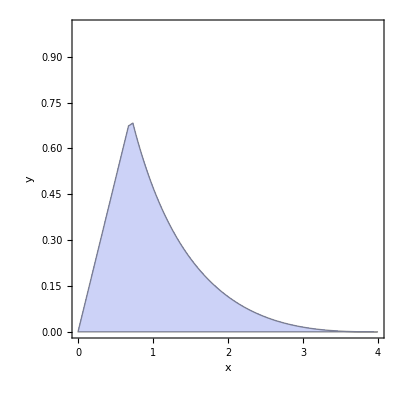
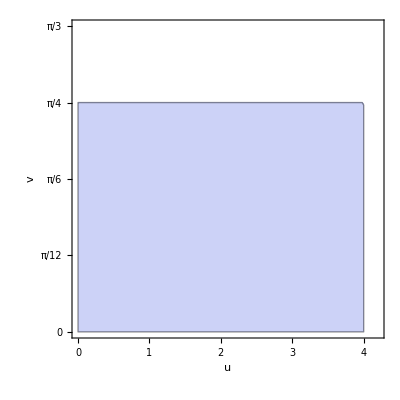
Dominio Ω | Imagen bajo T
-Graphics- | -Graphics-

El determinante del Jacobiano es: | 5 u Cos[v]^6 Sin[v]^4+5 u Cos[v]^4 Sin[v]^6

El valor de la integral planteada es: | 0.106289

El valor del area de Ω es: | 0.736311

```mathematica
Clear[f,g,transf,jac];
f[x_,y_]=x^(2/5)+y^(2/5)-alfa^(2/5);
g[x_,y_]=y-x;

(* Definimos la región de integración Ω *)
omega = RegionPlot[x^(2/5)+y^(2/5)≤ alfa^(2/5)&&0≤y≤x,{x,0,4},{y,0,1},FrameLabel->{x,y},RotateLabel->False];

(* Definimos la región de integración bajo la transformacion T *)
transf =RegionPlot[u^(2/5)≤alfa^(2/5)&& v ≥0 && v ≤ 2 π&& u*Sin[v]^5≥0&& u*Cos[v]^5≥0 && u*Sin[v]^5≤u*Cos[v]^5,{u,0,alfa+0.2},{v,0,π/4+π/12},FrameLabel->{u,v},RotateLabel->False,FrameTicks->{Automatic,Range[0,π/3,π/12],None,None}];

(* Graficamos las regiones *)
Grid[{{"Dominio Ω","Imagen bajo T"},{omega,transf}}]

(* La matriz Jacobiana *)
jac =Det[({{D[(u*Cos[v]^5), u], D[(u*Sin[v]^5), u]}, {D[(u*Cos[v]^5), v], D[(u*Sin[v]^5), v]}})];
Grid[{{"El determinante del Jacobiano es:",jac}}]

(* Calcular la integral sobre Ω, es lo mismo que calcularla bajo T *)
resb =N[∫_0^4 ∫_0^(π/4) ((alfa^(2/5)-u^(2/5))^2*jac)ⅆvⅆu];
Grid[{{"El valor de la integral planteada es:",resb}}]

(* Calcular el area de Ω, pero lo hremos bajo T *)
resc =N[∫_0^4 ∫_0^(π/4) (jac)ⅆvⅆu];
Grid[{{"El valor del area de Ω es:",resc}}]
```